```mathematica
dir=NotebookDirectory[];
```

## Data

### PS

```mathematica
udPS=Import[dir<>"data_meson_EFFs_PS/udPS.dat"];
usPS=Import[dir<>"data_meson_EFFs_PS/usPS.dat"];
dsPS=Import[dir<>"data_meson_EFFs_PS/dsPS.dat"];
cdPS=Import[dir<>"data_meson_EFFs_PS/cdPS.dat"];
cuPS=Import[dir<>"data_meson_EFFs_PS/cuPS.dat"];
ubPS=Import[dir<>"data_meson_EFFs_PS/ubPS.dat"];
dbPS=Import[dir<>"data_meson_EFFs_PS/dbPS.dat"];
csPS=Import[dir<>"data_meson_EFFs_PS/csPS.dat"];
sbPS=Import[dir<>"data_meson_EFFs_PS/sbPS.dat"];
cbPS=Import[dir<>"data_meson_EFFs_PS/cbPS.dat"];
```

### VC_G_E

```mathematica
udVC1=Import[dir<>"data_meson_EFFs_VC/udVC1.dat"];
usVC1=Import[dir<>"data_meson_EFFs_VC/usVC1.dat"];
dsVC1=Import[dir<>"data_meson_EFFs_VC/dsVC1.dat"];
cdVC1=Import[dir<>"data_meson_EFFs_VC/cdVC1.dat"];
cuVC1=Import[dir<>"data_meson_EFFs_VC/cuVC1.dat"];
ubVC1=Import[dir<>"data_meson_EFFs_VC/ubVC1.dat"];
dbVC1=Import[dir<>"data_meson_EFFs_VC/dbVC1.dat"];
csVC1=Import[dir<>"data_meson_EFFs_VC/csVC1.dat"];
sbVC1=Import[dir<>"data_meson_EFFs_VC/sbVC1.dat"];
cbVC1=Import[dir<>"data_meson_EFFs_VC/cbVC1.dat"];
```

### VC_G_M

```mathematica
udVC2=Import[dir<>"data_meson_EFFs_VC/udVC2.dat"];
usVC2=Import[dir<>"data_meson_EFFs_VC/usVC2.dat"];
dsVC2=Import[dir<>"data_meson_EFFs_VC/dsVC2.dat"];
cdVC2=Import[dir<>"data_meson_EFFs_VC/cdVC2.dat"];
cuVC2=Import[dir<>"data_meson_EFFs_VC/cuVC2.dat"];
ubVC2=Import[dir<>"data_meson_EFFs_VC/ubVC2.dat"];
dbVC2=Import[dir<>"data_meson_EFFs_VC/dbVC2.dat"];
csVC2=Import[dir<>"data_meson_EFFs_VC/csVC2.dat"];
sbVC2=Import[dir<>"data_meson_EFFs_VC/sbVC2.dat"];
cbVC2=Import[dir<>"data_meson_EFFs_VC/cbVC2.dat"];
```

### VC_G_Q

```mathematica
udVC3=Import[dir<>"data_meson_EFFs_VC/udVC3.dat"];
usVC3=Import[dir<>"data_meson_EFFs_VC/usVC3.dat"];
dsVC3=Import[dir<>"data_meson_EFFs_VC/dsVC3.dat"];
cdVC3=Import[dir<>"data_meson_EFFs_VC/cdVC3.dat"];
cuVC3=Import[dir<>"data_meson_EFFs_VC/cuVC3.dat"];
ubVC3=Import[dir<>"data_meson_EFFs_VC/ubVC3.dat"];
dbVC3=Import[dir<>"data_meson_EFFs_VC/dbVC3.dat"];
csVC3=Import[dir<>"data_meson_EFFs_VC/csVC3.dat"];
sbVC3=Import[dir<>"data_meson_EFFs_VC/sbVC3.dat"];
cbVC3=Import[dir<>"data_meson_EFFs_VC/cbVC3.dat"];
```

## Plot_charged (Figure 5)

### π, ρ

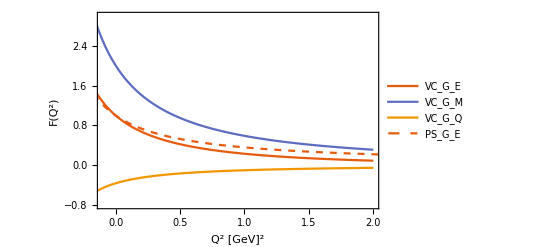

```mathematica
ListLinePlot[{udVC1,udVC2,udVC3,udPS},PlotRange->{{-0.1,2},{-0.8,3}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

### K^+, K^+*

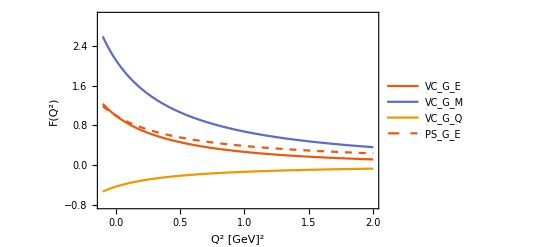

```mathematica
ListLinePlot[{usVC1,usVC2,usVC3,usPS},PlotRange->{{-0.1,2},{-0.8,3}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

### D^+, D^+*

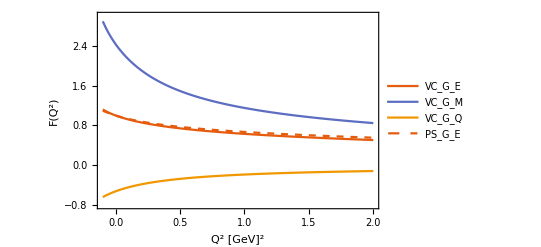

```mathematica
ListLinePlot[{cdVC1,cdVC2,cdVC3,cdPS},PlotRange->{{-0.1,2},{-0.8,3}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

### D_s, D^*_s

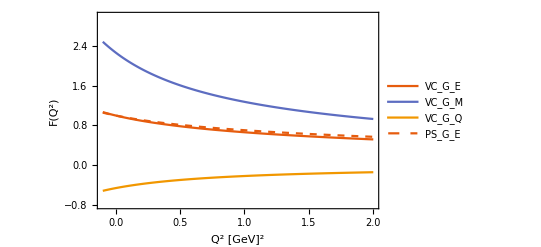

```mathematica
ListLinePlot[{csVC1,csVC2,csVC3,csPS},PlotRange->{{-0.1,2},{-0.8,3}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

### B^+,B^*+

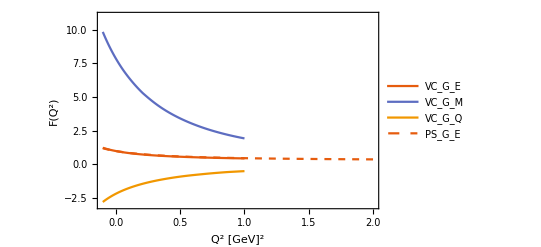

```mathematica
ListLinePlot[{ubVC1,ubVC2,ubVC3,ubPS},PlotRange->{{-0.1,2},{-3,11}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

### B_c,B^*_c

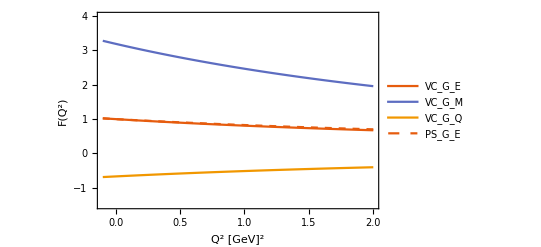

```mathematica
ListLinePlot[{cbVC1,cbVC2,cbVC3,cbPS},PlotRange->{{-0.1,2},{-1.5,4}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

## Plot_neutral (Figure 6)

### K^0, K^*0

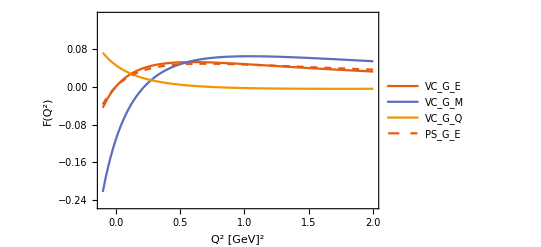

```mathematica
ListLinePlot[{dsVC1,dsVC2,dsVC3,dsPS},PlotRange->{{-0.1,2},{-0.25,0.15}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

### D^0,D^*0

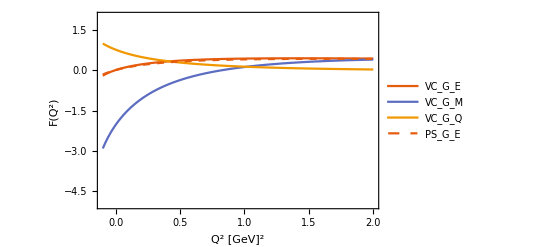

```mathematica
ListLinePlot[{cuVC1,cuVC2,cuVC3,cuPS},PlotRange->{{-0.1,2},{-5,2}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

### B^*, B^*0

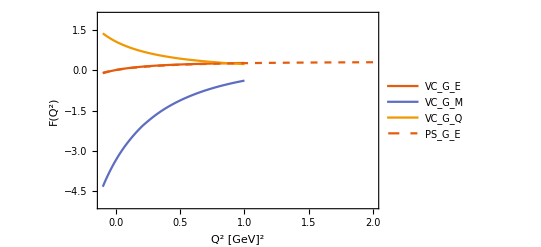

```mathematica
ListLinePlot[{dbVC1,dbVC2,dbVC3,dbPS},PlotRange->{{-0.1,2},{-5,2}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```

### B_s, B^*_s

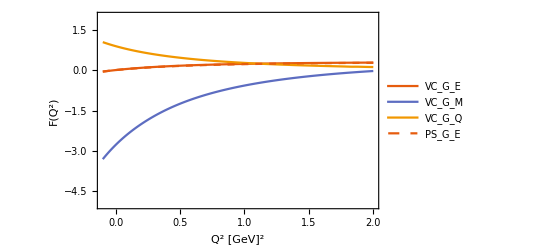

```mathematica
ListLinePlot[{sbVC1,sbVC2,sbVC3,sbPS},PlotRange->{{-0.1,2},{-5,2}},PlotStyle->{
{Line,ColorData[108,1]},{Line,ColorData[108,2]},{Line,ColorData[108,3]},{Dashed,ColorData[108,1]}},PlotLegends->{"VC_G_E","VC_G_M","VC_G_Q","PS_G_E"},Frame->True,FrameLabel->{"Q^2 [GeV]^2","F(Q^2)"}]
```